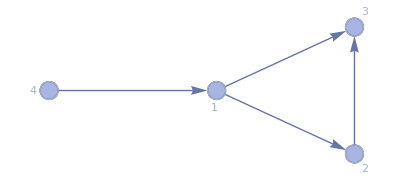

```mathematica
ResourceFunction["WolframModelPlot"][{{1,2},{1,3},{2,3},{4,1}},VertexLabels->Automatic]
```

```mathematica
GraphicsGrid[Partition[Labeled[Framed[ResourceFunction["WolframModelPlot"][ResourceFunction["WolframModel"][#,{{1}},4,"FinalState"],ImageSize->140],FrameStyle->LightGray],RulePlot[ResourceFunction["WolframModel"][#],ImageSize->Tiny,"RulePartsAspectRatio"->1]]&/@{{{x}}->{{x,x},{x},{x}},{{x}}->{{x,x},{x},{y}},{{x}}->{{x,x},{y},{y}},{{x}}->{{x,x},{y},{z}},{{x}}->{{x,y},{x},{x}},{{x}}->{{x,y},{x},{y}},{{x}}->{{x,y},{y},{y}},{{x}}->{{x,y},{y},{z}},{{x}}->{{y,x},{x},{x}},{{x}}->{{y,x},{x},{y}},{{x}}->{{y,x},{y},{y}},{{x}}->{{y,x},{y},{z}},{{x}}->{{y,y},{x},{x}},{{x}}->{{y,y},{x},{y}},{{x}}->{{y,y},{y},{y}},{{x}}->{{y,y},{y},{z}}},4],ImageSize->Full,Spacings->{20,10},Alignment->Bottom]
```

Global`WolframModelEvolutionObject::shdw: Symbol WolframModelEvolutionObject appears in multiple contexts {Global`,SetReplace`}; definitions in context Global` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
signature={{1,2}}->{{3,2}};
rule=RandomChoice[rf["EnumerateWolframModelRules"][signature]];
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

```mathematica
states=rf["WolframModel"][rule,{{0,0}},5,"StatesList"];
```

```mathematica
Animate[rf["WolframModelPlot"][state], {state, states}]
```

```mathematica
Module[{rules=ResourceFunction["EnumerateWolframModelRules"][{{1,2}}->{{3,2}}],res},res=ParallelMap[ResourceFunction["WolframModel"][#,{{0,0}},5,"FinalState"]&,rules];GraphicsGrid[Partition[ResourceFunction["WolframModelPlot"]/@DeleteDuplicates[Select[res,ConnectedGraphQ[Graph[UndirectedEdge@@@#]]&]],UpTo[15]],ImageSize->Full]]
```

ResourceFunction::usermessage: ParallelMapMonitored

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

-Graphics-

```mathematica
Module[{rules=ResourceFunction["EnumerateWolframModelRules"][{{1,2}}->{{2,2},{1,3}}],res},res=ParallelMap[ResourceFunction["WolframModel"][#,{{0,0}},5,"FinalState"]&,rules];GraphicsGrid[Partition[ResourceFunction["WolframModelPlot"]/@DeleteDuplicates[Select[res,ConnectedGraphQ[Graph[UndirectedEdge@@@#]]&]],UpTo[15]],ImageSize->Full]]
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

$Aborted

```mathematica
rf=ResourceFunction
```

ResourceFunction

```mathematica
rules = rf["EnumerateWolframModelRules"][{{1,2}}->{{3,2}}]
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

{{{1,1}}→{{1,1},{1,1},{1,1}},{{1,1}}→{{1,1},{1,1},{1,2}},{{1,1}}→{{1,1},{1,1},{2,1}},{{1,1}}→{{1,1},{1,2},{1,2}},{{1,1}}→{{1,1},{1,2},{2,1}},{{1,1}}→{{1,1},{1,2},{2,2}},{{1,1}}→{{1,1},{1,2},{1,3}},{{1,1}}→{{1,1},{1,2},{2,3}},{{1,1}}→{{1,1},{1,2},{3,1}},{{1,1}}→{{1,1},{1,2},{3,2}},486,{{1,2}}→{{3,4},{3,5},{1,3}},{{1,2}}→{{3,4},{3,5},{1,4}},{{1,2}}→{{3,4},{3,5},{2,3}},{{1,2}}→{{3,4},{3,5},{2,4}},{{1,2}}→{{3,4},{3,5},{4,1}},{{1,2}}→{{3,4},{3,5},{4,2}},{{1,2}}→{{3,4},{4,5},{1,5}},{{1,2}}→{{3,4},{4,5},{2,5}},{{1,2}}→{{3,4},{4,5},{5,1}},{{1,2}}→{{3,4},{4,5},{5,2}}}
 |  |  |  |

```mathematica
wfm=ResourceFunction["WolframModel"]
```

```mathematica
enumerateRules = ResourceFunction["EnumerateWolframModelRules"]
```

```mathematica
enumerateRules[{{1,2}}->{{2,2}}] // Length
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

73

```mathematica
signature = {{1,2}}->{{2,2}}
```

{{1,2}}→{{2,2}}

```mathematica
enumerateRules[signature]
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

{{{1,1}}→{{1,1},{1,1}},{{1,1}}→{{1,1},{1,2}},{{1,1}}→{{1,1},{2,1}},{{1,1}}→{{1,2},{1,2}},{{1,1}}→{{1,2},{2,1}},{{1,1}}→{{1,2},{1,3}},{{1,1}}→{{1,2},{2,3}},{{1,1}}→{{1,2},{3,2}},{{1,1}}→{{2,1},{2,1}},{{1,1}}→{{2,2},{1,2}},{{1,1}}→{{2,2},{2,1}},{{1,1}}→{{2,1},{1,3}},{{1,1}}→{{2,1},{2,3}},{{1,1}}→{{2,1},{3,1}},{{1,1}}→{{2,3},{3,1}},{{1,2}}→{{1,1},{1,1}},{{1,2}}→{{1,1},{1,2}},{{1,2}}→{{1,1},{2,1}},{{1,2}}→{{1,1},{2,2}},{{1,2}}→{{1,2},{1,2}},{{1,2}}→{{1,2},{2,1}},{{1,2}}→{{2,1},{2,1}},{{1,2}}→{{2,2},{1,2}},{{1,2}}→{{2,2},{2,1}},{{1,2}}→{{2,2},{2,2}},{{1,2}}→{{1,1},{1,3}},{{1,2}}→{{1,1},{2,3}},{{1,2}}→{{1,2},{1,3}},{{1,2}}→{{1,2},{2,3}},{{1,2}}→{{2,1},{1,3}},{{1,2}}→{{2,1},{2,3}},{{1,2}}→{{2,2},{1,3}},{{1,2}}→{{2,2},{2,3}},{{1,2}}→{{1,1},{3,1}},{{1,2}}→{{1,1},{3,2}},{{1,2}}→{{1,2},{3,2}},{{1,2}}→{{2,1},{3,1}},{{1,2}}→{{2,2},{3,1}},{{1,2}}→{{2,2},{3,2}},{{1,2}}→{{1,3},{1,3}},{{1,2}}→{{1,3},{2,3}},{{1,2}}→{{1,3},{3,1}},{{1,2}}→{{1,3},{3,2}},{{1,2}}→{{2,3},{2,3}},{{1,2}}→{{2,3},{3,1}},{{1,2}}→{{2,3},{3,2}},{{1,2}}→{{1,3},{1,4}},{{1,2}}→{{1,3},{2,4}},{{1,2}}→{{1,3},{3,4}},{{1,2}}→{{2,3},{2,4}},{{1,2}}→{{2,3},{3,4}},{{1,2}}→{{1,3},{4,2}},{{1,2}}→{{1,3},{4,3}},{{1,2}}→{{2,3},{4,1}},{{1,2}}→{{2,3},{4,3}},{{1,2}}→{{3,1},{1,2}},{{1,2}}→{{3,1},{3,1}},{{1,2}}→{{3,1},{3,2}},{{1,2}}→{{3,2},{2,1}},{{1,2}}→{{3,2},{3,2}},{{1,2}}→{{3,3},{1,3}},{{1,2}}→{{3,3},{2,3}},{{1,2}}→{{3,3},{3,1}},{{1,2}}→{{3,3},{3,2}},{{1,2}}→{{3,1},{1,4}},{{1,2}}→{{3,1},{3,4}},{{1,2}}→{{3,2},{2,4}},{{1,2}}→{{3,2},{3,4}},{{1,2}}→{{3,1},{4,1}},{{1,2}}→{{3,1},{4,2}},{{1,2}}→{{3,2},{4,2}},{{1,2}}→{{3,4},{4,1}},{{1,2}}→{{3,4},{4,2}}}